```mathematica
ClearAll[x,y,z,flukaDataIP]
```

```mathematica
flukaData=Import["/home/hovanes/Documents/Wolfram Mathematica/CPS_Temperature_With_Mathematica/klcps59_31b.bnn.lis.table.csv","CSV"]
```

{{0.0125,-3.11978,0.25,0.0564},{0.0125,-3.11978,0.75,0.092305},{0.0125,-3.11978,1.25,0.16194},{0.0125,-3.11978,1.75,0.27497},{0.0125,-3.11978,2.25,0.39391},{0.0125,-3.11978,2.75,0.5447},{0.0125,-3.11978,3.25,0.6541},{0.0125,-3.11978,3.75,0.8145},{0.0125,-3.11978,4.25,0.97875},8663023,{7.9875,3.11978,90.25,7.831×10^-7},{7.9875,3.11978,90.75,3.2676×10^-6},{7.9875,3.11978,91.25,1.67815×10^-6},{7.9875,3.11978,91.75,1.25965×10^-6},{7.9875,3.11978,92.25,3.5989×10^-7},{7.9875,3.11978,92.75,2.94005×10^-11},{7.9875,3.11978,93.25,2.36965×10^-6},{7.9875,3.11978,93.75,1.47475×10^-6}}
 |  |  |  |

```mathematica
flukaDataIP=Interpolation[flukaData, InterpolationOrder->1]
```

InterpolatingFunction[{{0.0125, 7.9875}, {-3.11978, 3.11978}, {0.25, 93.75}}, <>]

```mathematica
flukaDataIP[1,1,1]
```

0.0011778

InterpolatingFunction::dmval: Input value {0.36,-3.14146,2.0018} lies outside the range of data in the interpolating function. Extrapolation will be used.

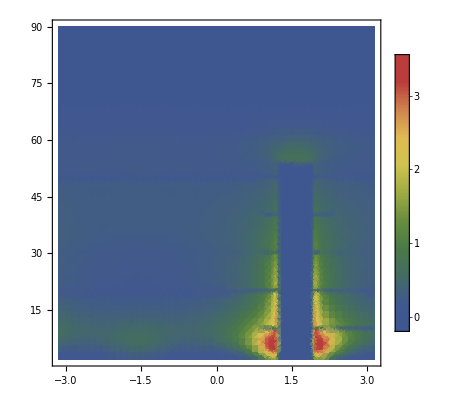

```mathematica
DensityPlot[flukaDataIP[0.36,ϕ,z], {ϕ,-π,π}, {z,2, 90},PlotRange->Full,ColorFunction->{"DarkRainbow"},PlotLegends->Automatic,ScalingFunctions->{Identity,Identity,Identity}, PlotPoints->50]
```

InterpolatingFunction::dmval: Input value {0.000122449,(4 π)/9,2.0018} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.,(4 π)/9,5.14286} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.,(4 π)/9,4.91837} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

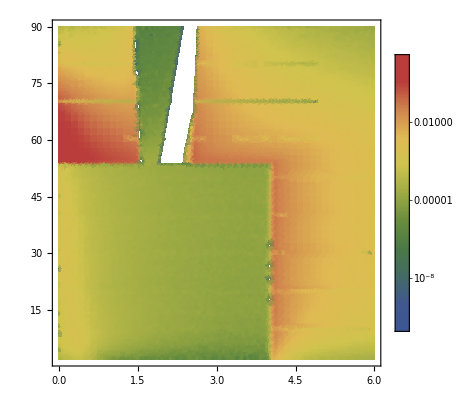

```mathematica
DensityPlot[flukaDataIP[r,8/18*π,z], {r,0,6}, {z,2, 90}, PlotRange->Full,ColorFunction->{"DarkRainbow"},PlotLegends->Automatic,ScalingFunctions->{Identity,Identity,"Log"}, PlotPoints->50]
```

```mathematica
Export["/home/hovanes/Documents/Wolfram\ Mathematica/CPS_Temperature_With_Mathematica/klcps59_31b_Order1.m" , flukaDataIP]
```

/home/hovanes/Documents/Wolfram Mathematica/CPS_Temperature_With_Mathematica/klcps59_31b_Order1.m